{A_0→7/18,A_1→99/16,A_2→-16/5,B_0→-154/9,B_1→29/4,B_2→32}

{-790/9-(259 X)/18+(7 X^2)/18,5+32 X+(99 X^2)/16,5+32 X-(16 X^2)/5}

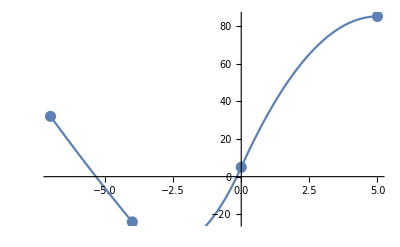

```mathematica
Subscript[x, 0]=-7;Subscript[x, 1]=-4;Subscript[x, 2]=0;Subscript[x, 3]=5;
Subscript[f, 0]= 32;Subscript[f, 1]=-24;Subscript[f, 2]=5;Subscript[f, 3]=85;
n=3;
Subscript[P, k_][X_]=Subscript[f, k]+ (X-Subscript[x, k])(Subscript[A, k] X+Subscript[B, k]);
eq1=Table[Subscript[P, k][Subscript[x, k+1]]==Subscript[P, k+1][Subscript[x, k+1]],{k,0,n-2}];
eq2={Subscript[P, n-1][Subscript[x, n]]==Subscript[f, n]};
Subscript[PP, k_][X_]=D[Subscript[P, k][X], X];
eq3=Table[Subscript[PP, k][Subscript[x, k+1]]==Subscript[PP, k+1][Subscript[x, k+1]],{k,0,n-2}];
eq4={Subscript[PP, n-1][Subscript[x, n]]==0};
eq=Join[eq1,eq2,eq3,eq4];
koef=Solve[eq,{}]//Flatten
Spl[X_]=Table[Subscript[P, k][X]/.koef,{k,0,n-1}]//Expand
Tb1=Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}];
Gr1= ListPlot[Tb1,PlotStyle->{PointSize[0.02]}];
Gr2=Table[Plot[Spl[X][[k]],{X,Subscript[x, k-1],Subscript[x, k]}],{k,1,n}];
Show[Gr1,Gr2]
```